```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
NormXAxis[data_]:={(Range[Length[data]]-1)/Length[data],data}ᵀ;
GF=GaussianFilter[#,10]&;
R=RotateRight;
Der[f_,dx_]:=(R[f,1]-R[f,-1])/(2 dx)
Lap[f_,dx_]:=(R[f,1]-2f+R[f,-1])/dx/dx
```

```mathematica
GetSimData[dir_,s_]:=Block[{info},
info=<|(#1->#2)&@@@Import[dir<>"/SheetSimulation.info"]⟦;;,{1,3}⟧|>;
Return[<| 
"info"->info,
"ρ"->ArrayReshape[Import[dir<>"/strips_density.strip.gz","Table"],{s,1*info["nx"]}],
"x"->ArrayReshape[Import[dir<>"/strips_x.strip.gz","Table"],{s,info["ns1"]}],
"dϕ"->ArrayReshape[Import[dir<>"/strips_d_phi.strip.gz","Table"],{s,info["nx"]}],
"v"->ArrayReshape[Import[dir<>"/strips_vx.strip.gz","Table"],{s,info["ns1"]}],
"ϕ"->ArrayReshape[Import[dir<>"/strips_phi.strip.gz","Table"],{s,info["nx"]}],
"M"->Import[dir<>"/constraints.dat.gz"]⟦;;,1⟧,
"E"->Import[dir<>"/constraints.dat.gz"]⟦;;,2⟧
|>]
];
```

```mathematica
dirs=DeleteDuplicates[DirectoryName/@FileNames["*/SheetSimulation.info"]];
data=<|Table[dir->GetSimData[dir,400],{dir,dirs}]|>;
```

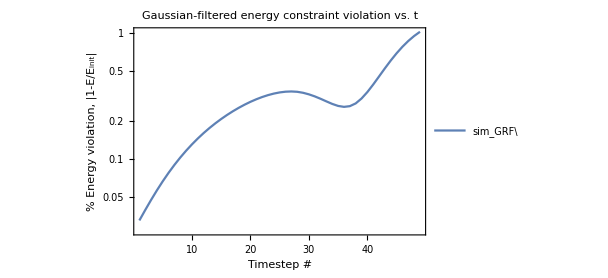

```mathematica
plot=ListLogPlot[
GF/@Table[Abs[1-data[k]["E"]⟦n⟧/data[k]["E"]⟦1⟧],{k,Keys[data]},{n,2,50}],
Joined->True,PlotRange->All,PlotLegends->Keys[data],Axes->False,Frame->True, FrameLabel->{"Timestep #", "% Energy violation, |1-E/E_init|"},ImageSize->450,PlotLabel->"Gaussian-filtered energy constraint violation vs. t"
]
```

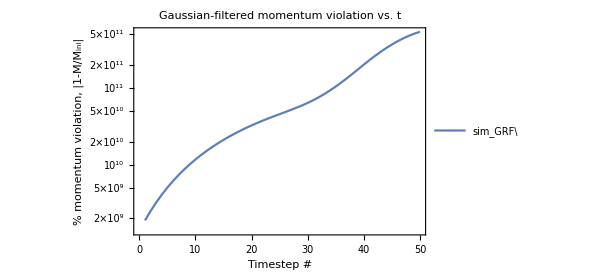

```mathematica
plot=ListLogPlot[
GF/@Table[Abs[data[k]["M"]⟦n⟧/data[k]["M"]⟦1⟧-1],{k,Keys[data]},{n,1,50}],
Joined->True,PlotRange->All,PlotLegends->Keys[data],Axes->False,Frame->True, FrameLabel->{"Timestep #", "% momentum violation, |1-M/M_ini|"},ImageSize->450,PlotLabel->"Gaussian-filtered momentum violation vs. t"
]
(*plot=ListLogPlot[
GF/@Table[Abs[data[k]["M"]⟦n⟧],{k,Keys[data]},{n,1,400}],
Joined->True,PlotRange->All,PlotLegends->Keys[data],Axes->False,Frame->True, FrameLabel->{"Timestep #", "Absolute momentum violation, |M|"},ImageSize->450,PlotLabel->"Gaussian-filtered momentum violation vs. t"
]*)
```

```mathematica
Manipulate[
ListPlot[Table[NormXAxis[data[k]["ρ"]⟦n⟧],{k,Keys[data]}],Joined->True,PlotRange->All,PlotLegends->Keys[data],ImageSize->700],
{n,1,400,1}
]
```

```mathematica
Manipulate[
Show[
ListPlot[Table[{data[k]["x"]⟦n⟧,data[k]["v"]⟦n⟧}ᵀ,{k,Keys[data]}],Joined->True,PlotRange->All,PlotLegends->Keys[data],ImageSize->700],
ListPlot[Table[{data[k]["x"]⟦n⟧,data[k]["v"]⟦n⟧}ᵀ,{k,Keys[data]}],Joined->False,PlotRange->All]
],
{n,1,50,1}
]
```

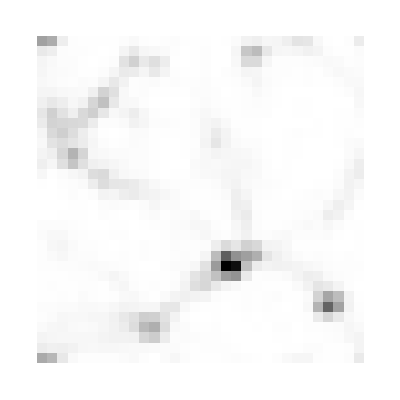

```mathematica
ρfield=ArrayReshape[Import["sim_GRF/step_100_density.dat.gz"],{32,32,32}];
ArrayPlot[ρfield⟦5⟧]
```